# Parser for FHI-AIMS LCAO coefficients file of cluster

If the AIMS calculation is not performed in periodic boundary conditions, then the whole LCAO coef. file is crazily parsed. This is an old way how to put it into “Fireball-like” files. For these calculations it was also necessary to print basis to get +/- coefficients of the basis far-away from nuclei.
Modern parser in PP-STM working for PBC-calculations do all the +/- coef. calculations automatically.

```mathematica
path=(*"~/Desktop/Luna/AIMS_mol/TOAT_old/Cluster_lda/";*)"~/Desktop/WORK/probe_particle_code/TAP_cluster/";
inp=Import[path<>"/KS_eigenvectors_sh.out","Table"];
eigen=Drop[Import[path<>"/all_states_sh.dat","Table",HeaderLines->1],-2];
maxOrb=Max[eigen[[All,1]]]
geom=Import[path<>"/geometry.in","Table"][[All,5]];
```

13400

```mathematica
(*maxOrb=1500*)
```

1500

```mathematica
numBasis=13552;(*|Total number of basis functions:*)
```

```mathematica
header=inp[[Range[2,numBasis+1],Range[2,6]]];
coefsi[i_]:=Quotient[i-1,5]*(numBasis+2)+Range[2,numBasis+1]
coefsj[i_]:=7+Mod[i-1,5]
```

```mathematica
For[j=1,j≤Length[eigen],j++,If[eigen[[j,4]]>-8.583(*-10*),{n1=j,Print[j],Break[]}]]
For[j=n1,j≤Length[eigen],j++,If[eigen[[j,4]]>-2.583(*5*),{n2=j,Print[j],Break[]},n2=numBasis]]
n2-n1+1
```

459

1304

846

```mathematica
lcaocoefs=Array[Null,{n2-n1+1}];
For[j=n1,j≤n2,j++,{lcaocoefs[[j-n1+1]]=inp[[coefsi[j],coefsj[j]]]}]
```

```mathematica
species={"Au","N","C","H","O"};
```

```mathematica
lmax={1,2,2,1,1,1,4};
o[1]:="_s.dat"
o[2]:="_p.dat"
o[3]:="_d.dat"
For[i=1,i≤Length[species],i++,{n[i_]:=ElementData[species[[i]],"Period"]}]
name[i_,k_,l_]:=path<>"/at_"<>ToString[i]<>"_"<>ToString[k]<>"_"<>ToString[n[i]]<>o[l];

For[i=1,i≤Length[species],i++,{For[l=1,l≤lmax[[n[i]]],l++,{(*Print[name[i,I,l]],*)For[k=1,k≤100,k++,If[FileExistsQ[name[i,k,l]],{Print[name[i,k,l]],R[i,l]=Import[name[i,k,l],"Table",HeaderLines->1]}]]}]}]
```

~/Desktop/WORK/probe_particle_code/TAP_cluster//at_1_6_6_s.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//at_2_16_2_s.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//at_2_17_2_p.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//at_3_19_2_s.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//at_3_20_2_p.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//at_4_21_1_s.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//at_5_23_2_s.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//at_5_24_2_p.dat

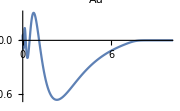
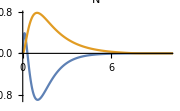
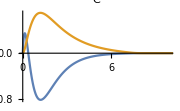
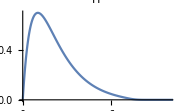
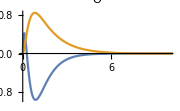

```mathematica
Table[{ListLinePlot[Table[R[i,l],{l,1,lmax[[n[i]]]}],PlotRange->{{0,10},All},PlotLabel->species[[i]],LabelStyle->Directive[Black,8],ImageSize->Small,PlotLegends->{"s","p","d}"}]},{i,1,Length[species]}]//TableForm
```

```mathematica
point=6;
For[i=1,i≤Length[species],i++,For[l=1,l≤lmax[[n[i]]],l++,For[k=1,k≤Length[R[i,l]],k++,{tmp=R[i,l];If[tmp[[k,1]]≤6,sign[i,l]=Sign[tmp[[k,2]]]]}]]];
tmp=.;Table[Table[sign[i,l],{l,1,lmax[[n[i]]]}],{i,1,Length[species]}]//TableForm
```

-1 | 
-1 | 1
-1 | 1
1 | 
-1 | 1

```mathematica
sign[4,1]=-0.5;sign[4,2]=0.5(*0.75*);(*oxygens to zero*)
Table[Table[sign[i,l],{l,1,lmax[[n[i]]]}],{i,1,Length[species]}]//TableForm
```

1 | 
-1 | 1
-1 | 1
-0.5 | 0.5
-1 |

```mathematica
atspec=geom;For[i=1,i<=Length[geom],i++,For[j=1,j≤Length[species],j++,If[species[[j]]==ToString[geom[[i]]],atspec[[i]]=j]]];
atspec[[Range[1,10]]]//TableForm
```

4
3
3
3
3
4
3
3
3
4

```mathematica
(*pos[jj,atom]*)
ai=1;
For[i=1,i≤numBasis,i++,If[ai>Length[geom],Break[],{If[header[[i,{1,2,3}]]=={ai,"atomic",n[atspec[[ai]]]},If[header[[i,4]]=="s",{pos[1,ai]=i,If[lmax[[n[atspec[[ai]]]]]==1,ai=ai+1]},If[lmax[[n[atspec[[ai]]]]]>1,{If[header[[i,{4,5}]]=={"p",-1},pos[2,ai]=i,If[header[[i,{4,5}]]=={"p",0},pos[3,ai]=i,If[header[[i,{4,5}]]=={"p",1},{pos[4,ai]=i,ai=ai+1}]]]},ai=ai+1]]]}]]
Print[ai-1]
Print[Length[geom]]
```

556

556

```mathematica
jjmax=4;(*sp*)
eig=eigen[[Range[n1,n2],4]];
TranCoefs=Array[Null,{jjmax,(n2-n1+1),Length[geom]*2+1}];
TranCoefs[[All,All,All]]=0.0;
For[i=1,i≤jjmax,i++,{TranCoefs[[i,All,1]]=eig[[All]]}];
tmp0=Length[eig];eig=.;
(*TranCoefs[[1,All,1]]//TableForm*)
TranCoefs[[1,{1,2,3,tmp0-2,tmp0-1,tmp0},1]]//TableForm
tmp0=.;
```

-8.5822
-8.57177
-8.56953
-2.69363
-2.66244
-2.5648

```mathematica
signJ={1,1,1,-1};(*Dont change, means - +s, +py +pz -px*)
For[jj=1,jj≤jjmax,jj++,{If[jj==1,l=1,If[jj≤4,l=2,{Print[problem],Break}]],For[ii=1,ii≤n2-n1+1,ii++,For[i=1,i≤Length[geom],i++,If[jj≤(lmax[[n[atspec[[i]]]]]^2),(*Print[jj," ",i," ",pos[jj,i]]*)TranCoefs[[jj,ii,2*i]]=lcaocoefs[[ii,pos[jj,i]]]*sign[atspec[[i]],l] *signJ[[jj]] (*,Print[i]*) ]]]}];
```

```mathematica
TableForm[TranCoefs[[1,Range[100,120],All]](*,TableDirections->Row*)](*Just for Checks*)
```

```mathematica
Prepend[TranCoefs[[1,All,All]],{Length[geom],n2-n1+1}]//TableForm (*Just for Checks*)
```

```mathematica
path="~/Documents/WORK/probe_particle_code/TAP_cluster_w_error"
```

~/Documents/WORK/probe_particle_code/TAP_cluster_w_error

```mathematica
Export[path<>"/phik_tier0_s.dat",Prepend[TranCoefs[[1,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_tier0_py.dat",Prepend[TranCoefs[[2,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_tier0_pz.dat",Prepend[TranCoefs[[3,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_tier0_px.dat",Prepend[TranCoefs[[4,All,All]],{Length[geom],n2-n1+1}],"Table"]
```

~/Desktop/WORK/probe_particle_code/TAP_cluster//phik_tier0_s.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//phik_tier0_py.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//phik_tier0_pz.dat

~/Desktop/WORK/probe_particle_code/TAP_cluster//phik_tier0_px.dat

```mathematica
sign[4,1]=0.0(*-0.25*);sign[4,2]=0.0(*0.25*);(*oxygens to zero*)
Table[Table[sign[i,l],{l,1,lmax[[n[i]]]}],{i,1,Length[species]}]//TableForm
```

1 | 
-1 | 1
-1 | 1
0. | 0.

```mathematica
atspec=geom;For[i=1,i<=Length[geom],i++,For[j=1,j≤Length[species],j++,If[species[[j]]==ToString[geom[[i]]],atspec[[i]]=j]]];
atspec[[Range[1,10]]]//TableForm

(*pos[jj,atom]*)
ai=1;
For[i=1,i≤numBasis,i++,If[ai>Length[geom],Break[],{If[header[[i,{1,2,3}]]=={ai,"atomic",n[atspec[[ai]]]},If[header[[i,4]]=="s",{pos[1,ai]=i,If[lmax[[n[atspec[[ai]]]]]==1,ai=ai+1]},If[lmax[[n[atspec[[ai]]]]]>1,{If[header[[i,{4,5}]]=={"p",-1},pos[2,ai]=i,If[header[[i,{4,5}]]=={"p",0},pos[3,ai]=i,If[header[[i,{4,5}]]=={"p",1},{pos[4,ai]=i,ai=ai+1}]]]},ai=ai+1]]]}]]
Print[ai-1]
Print[Length[geom]]
jjmax=4;(*sp*)
eig=eigen[[Range[n1,n2],4]];
TranCoefs=Array[Null,{jjmax,(n2-n1+1),Length[geom]*2+1}];
TranCoefs[[All,All,All]]=0.0;
For[i=1,i≤jjmax,i++,{TranCoefs[[i,All,1]]=eig[[All]]}];
eig=.;
(*TranCoefs[[1,All,1]]//TableForm*)
signJ={1,1,1,-1};(*Dont change, means - +s, +py +pz -px*)
For[jj=1,jj≤jjmax,jj++,{If[jj==1,l=1,If[jj≤4,l=2,{Print[problem],Break}]],For[ii=1,ii≤n2-n1+1,ii++,For[i=1,i≤Length[geom],i++,If[jj≤(lmax[[n[atspec[[i]]]]]^2),(*Print[jj," ",i," ",pos[jj,i]]*)TranCoefs[[jj,ii,2*i]]=lcaocoefs[[ii,pos[jj,i]]]*sign[atspec[[i]],l] *signJ[[jj]] (*,Print[i]*) ]]]}];

Export[path<>"/phik_0_4_s.dat",Prepend[TranCoefs[[1,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_0_4_py.dat",Prepend[TranCoefs[[2,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_0_4_pz.dat",Prepend[TranCoefs[[3,All,All]],{Length[geom],n2-n1+1}],"Table"]
Export[path<>"/phik_0_4_px.dat",Prepend[TranCoefs[[4,All,All]],{Length[geom],n2-n1+1}],"Table"]
```

3
2
2
2
2
2
2
2
2
2

34

34

/home/finarfin/Desktop/WORK/probe_particle_code/TOAT_aims/single_mol/symmetric_lda//phik_0_4_s.dat

/home/finarfin/Desktop/WORK/probe_particle_code/TOAT_aims/single_mol/symmetric_lda//phik_0_4_py.dat

/home/finarfin/Desktop/WORK/probe_particle_code/TOAT_aims/single_mol/symmetric_lda//phik_0_4_pz.dat

/home/finarfin/Desktop/WORK/probe_particle_code/TOAT_aims/single_mol/symmetric_lda//phik_0_4_px.dat

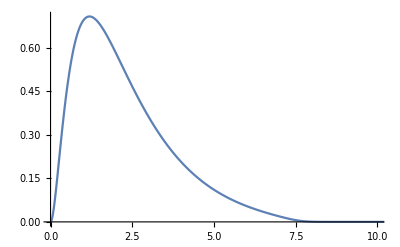

```mathematica
ListLinePlot[Import[path<>"/at_2_7_2_p.dat","Table",HeaderLines->1],PlotRange->{{0,10},All}]
```

```mathematica
"at_3_12_2_s.dat"
```

```mathematica
at11s=Import[path<>"/at_1_1_1_s.dat","Table",HeaderLines->1];
hy12s=Import[path<>"/hy_1_2_2_s.dat","Table",HeaderLines->1];
hy12p=Import[path<>"/hy_1_3_2_p.dat","Table",HeaderLines->1];
```

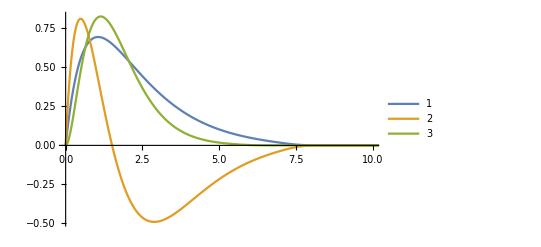

```mathematica
ListLinePlot[{at11s,hy12s,hy12p},PlotRange->{{0,10},All},PlotLegends->Automatic]
```

```mathematica
max={10^2,10^0,10^2,10^1};
min={10^-8,10^-9,10^-8,10^-9};
```

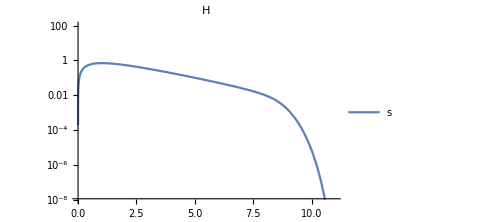
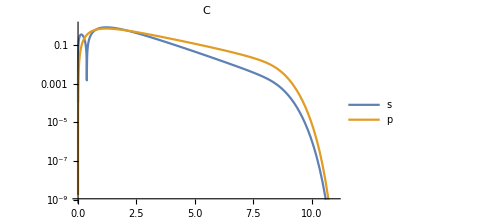
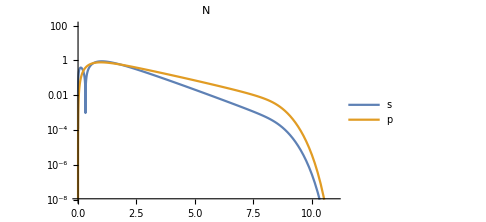
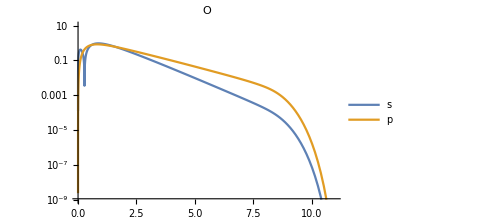

```mathematica
Table[{ListLogPlot[Table[Abs[R[i,l]],{l,1,lmax[[n[i]]]}],Joined->True,PlotRange->{{0,11},{min[[i]],max[[i]]}},PlotLabel->species[[i]],LabelStyle->Directive[Bold,12],ImageSize->Medium,PlotLegends->{"s","p","d}"}]},{i,1,Length[species]}]//TableForm
```

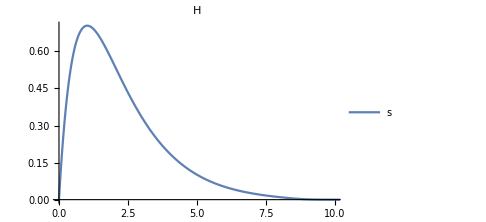
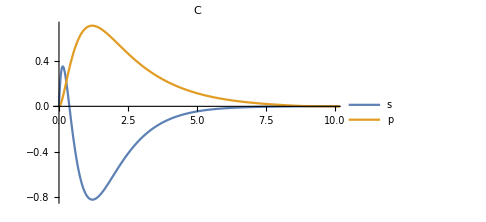
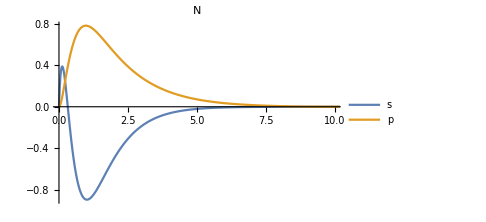
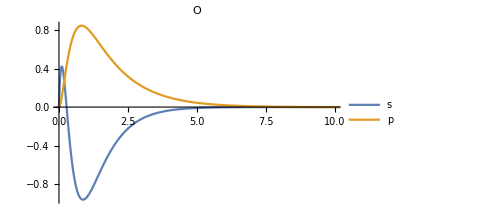

```mathematica
Table[{ListLinePlot[Table[R[i,l],{l,1,lmax[[n[i]]]}],PlotRange->{{0,10},All},PlotLabel->species[[i]],LabelStyle->Directive[Bold,12],ImageSize->Medium,PlotLegends->{"s","p","d}"}]},{i,1,Length[species]}]//TableForm
```